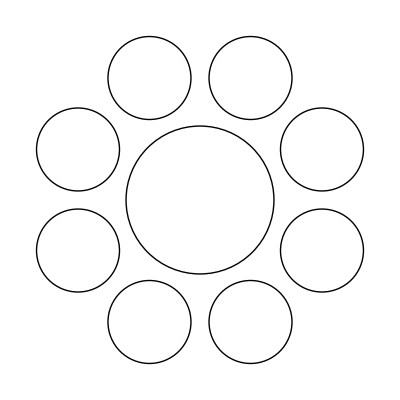

```mathematica
(* This function generates the {x,y} points that become the centres of the circles around the outside *)
circlePoints[K_]:=Table[{Cos[ (-π/2)+(k+1/2)*(2π/K)],Sin[(-π/2)+(k+1/2)*(2π/K)]},{k,0,K-1}]

(* this function combines a list of circles around the outside with a single circle in the centre to make the hand-pan shape *)
handPan[n_]:=Graphics[
Join[
Circle[(1.25n)#/π]&/@circlePoints[n],(* outside circles *)
{Circle[{0,0},((1.25n)/π)-1.4]} (* centre circle *)
]
]

(* generate the shape with eight notes *)
handPan[8]
```

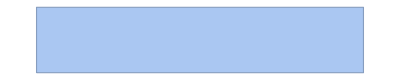

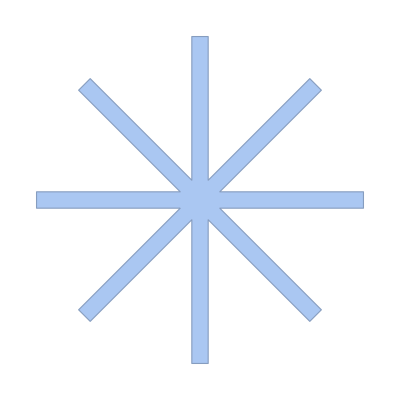

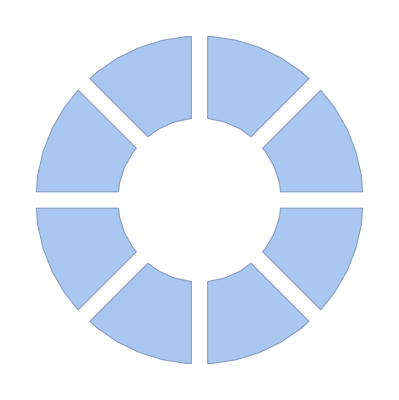

```mathematica
outerCircle = Disk[];
innerCirle = Disk[{0,0},0.5];
doughNut = BoundaryDiscretizeRegion[RegionDifference[outerCircle,innerCirle]];
cutter = BoundaryDiscretizeRegion[Rectangle[{-1,-0.05},{1,0.05}]]
cutterSet = RegionUnion[Table[Rotate[cutter,theta],{theta,0,π,π/4}]]
complexRegion = RegionDifference[doughNut,cutterSet]
```